# Learning Arduino

## Serial Input

Like CP3O in Star Wars, the Arduino speaks a variety of languages. I squared C, Pulse Wave Modulation, Analog, and serial protocols allow it to communicate to any number of devices, including another microcontroller or computer. We are going to use the Arduino’s ability to stream ASCII characters over a serial communication link to set up a conversation between the board’s microprocessor and Mathematica. Mathematica is a cool tool to visualize data streaming from an Arduino; It is a great interface to control devices through the Arduino.

There are three exercises in this investigation: Serial Input, Serial Output, and Creating an Interactive Project. In Serial Input we will use Mathematica to visualize data streaming from the Arduino over a serial link. In Serial Output we will use visual controls in Mathematica to command an actual physical device connected to the Arduino. Finally, in Creating an Interactive Project you will create an interactive ‘Etch-a-Sketch’ using an Arduino board, various components, and the Processing IDE.

Lab notebook Remember to document ALL of your work, especially coding and electronics, in your lab notebook. For specific instructions pertinent to this lesson, see the Lab notebook section at the end.

Safety Remember to ground yourself before handling the electronics. Static is bad, very bad.

## Serial Input

### Introduction

In this experiment we are going to connect a variable resistor or potentiometer (“pot” for short) to the Arduino board’s analog pins and convert the value from the potentiometer into an integer number that will stream over the serial link to a computer. On the computer’s side, we will capture this stream and use it to visually display the data stream. 

But what is a potentiometer? A “pot” creates variable resistance in an electronic circuit ranging from zero to some maxium, defined value. The greater the resistance, the more difficult it is for current to flow through a circuit. There are many different kinds of potentiometers. They vary by maximum resistance, by the amount of current they can safely handle, and by their response. Some pots have linear responses, while others have logorithmic responses. Pots come in a range of shapes and sizes. Pots are often used to control volume, brightness, or some other setting that needs to be adjusted by the user. Think of a mixing board.

You can use the multimeter, set to ohms, to determine the amount of resistance generated by a potentiometer. This can be done by connecting the leads of the multimeter to a potentiometer and moving the knob around. Resistance will vary between zero and the pot’s design maxiumum.

What you will need:

• An Arduino board
• A laptop
• A USB cable to connect the Arduino to the laptop
• The Arduino IDE
• Arduino example sketchs 5
• Mathematica
• A small breadboard
• A small breadboard compatible potentiometer
• Five patch wires (2 red, 2 black, and 1 yellow)

### Constructing the circuit

We want to construct a simple analog circuit like the one shown here. The potentiometer has three pins: ground (negative), voltage in (positive), and the “wiper” (the output). To connect the pot to the Arduino board you should first place it onto the breadboard. Each pin of the pot should be in a different row of the board so that they are electrically isolated. Connect the red and black leads to the outer pins of the potentiometer and the yellow lead to the middle pin. Unlike a diode or LED, the orientation of the pot does not matter here as long as one of the outer pins is the ground and the other outer pin is the positive connection. Connect the red lead to the +5v power pin on the Arduino, the black lead to the ground pin just next to the power pin, and the yellow lead to analog input A0. The pins should all be on the same side of the Arduino board as shown in the photograph below.

Please note that your potentiometer may look a bit different. They come in all shapes and sizes, but the idea is the same.

-Graphics-

Figure one: An Arduino connected to a small potentiometer via the analog input pins.

Here’s the circuit schematic:

Figure two: Circuit diagram of an Arduino connected to a small potentiometer via the analog input pins.

### Setting up the Arduino

Connect the Arduino to a laptop using the USB cable and start the Arduino IDE. Once the IDE is running, create a new sketch and save it into your Arduino sketch folder as “Exercise 5.”  Enter the code reproduced below into the window. Do not just copy and paste the code. Read and understand it.

Once you have added the code to your sketch, save it and then use the verify button to make sure that you have no mistakes (bugs). If the code checks out, upload it to the connected Arduino.

If all went well, the Arduino will have briefly flashed its on-board LED.

/*
Sage Ridge Robotics
Example 05
Streaming analog input values over a serial link

Code adapted from Adafruit, LLC
This code is in the Public Domain

*/
 
// Here we set the value of the variable potPin to an interger value, 0
int potPin = 0;

// In setup() we open the serial output for streaming 
// at a rate of 9600 characters per second
// We open the serial port for streaming by instantiating a serial object
// of the serial class.
void setup() 
{
  Serial.begin(9600);
}
 
// In the main loop we read the analog value of potPin every 500 milliseconds
// and stream the value out over the serial connection.
void loop() 
{
  int reading  = analogRead(potPin);
  Serial.println(reading);
  delay(100);
}

Arduino Sketch for Exercise 5, Serial Input.

### Verifying the Arduino’s stream

Let’s verify that the sketch is running correctly on the Arduino. The Arduino IDE has a serial monitor with which you can chat back and forth with the Arduino board. To open the serial monitor, click on the right most button on the tool bar.’ I’ve circled this button in blue in the image below.

Once you have opened the serial monitor window, you will see a stream of numbers. Try turning the knob on the potentiometer. You should see the numbers vary between a minimum (0) and a maximum (1023). The Arduino converts the analog voltage signal from the potentiometer, ranging from 0 to 5v, into a digital number.

Arduino Uno can convert the voltage to one of 1024 steps. That’s 4.9 mV (millivolts) per step. Pretty sensitive. 1024 steps because the Arduino works fundamentally in binary numbers, has a 10 bit-long register to convert the analog signal to digital, and because 1024 is 2^10. The value of the digital number representing the voltage from the pot ranges from 0000000000 to 1111111111.

Location of the Serial Monitor button on Arduinio IDE’s toolbar.

### Connecting the Arduino to Mathematica

You will need Mathematica 10 for this code to work. Mathematica 9 requires an external library more complex code to connect to and use a serial port. Use the code below, but replace the second parameter with your serial port address. For Windows, you will use “COM1,” “COM2,” or which ever COM port your Arduino is connected to. myArduino is the object instantiated to handle the connection. We will use the myArduino object to read data from and write data to the Arduino board. Remember to use shift+enter while the cursor is positioned in the cell with the DeviceOpen[] function to start the connection. The default connection parameters should correctly match the Arduino. If not, then you will have to add several options like baud rate, the number of characters per second.

```mathematica
myArduino = DeviceOpen["Serial","/dev/tty.usbmodemfa141"]
```

DeviceObject[…]

#### Test the connection

The first thing we want to do is to test the connection to see if there is any data streaming from the Arduino. The following command will return “True” if there is data in the serial buffer. Otherwise, the query will return “False.”

```mathematica
DeviceExecute[myArduino, "SerialReadyQ"]
```

DeviceExecute::ncdev: myArduino is not open.

$Failed

If the connection contains buffered data, we can read the serial data stream of the object we created above, myArduino, using DeviceRead[]. Notice how we pass the myArduino object to the function. Try moving the potentiometer around a bit and executing SerialRead below each time you make a change by turning the knob. What happens? What is the highest value returned from the pot? What is the lowest? DeviceRead[] returns a single integer value from the serial stream.

```mathematica
DeviceRead[myArduino]
```

51

DeviceReadBuffer[] will read all of the values in the current serial buffer. Try executing the command below a couple of times to see what happens.

```mathematica
DeviceReadBuffer[myArduino]
```

{53,52,48,13,10,53,52,48,13,10,53,51,57,13,10,53,52,48,13,10,53,51,57,13,10,53,51,57,13,10,53,51,57,13,10,53,52,48,13,10,53,51,57,13,10,53,51,57,13,10,53,51,57,13,10,53,51,57,13,10,53,51,57,13,10,53,51,57,13,10,53,51,57,13,10,53,51,57,13,10,53,52,48,13,10,53,51,57,13,10,53,51,57,13,10}

DeviceReadBuffer[object,n] allows you to choose the number of values returned. Try this code:

```mathematica
DeviceReadBuffer[myArduino, 100]
```

{53,52,48,13,10,53,51,57,13,10,53,51,57,13,10,53,51,57,13,10,53,51,57,13,10,53,51,57,13,10,53,51,57,13,10,53,51,57,13,10,53,52,48,13,10,53,52,48,13,10,53,52,48,13,10,53,52,48,13,10,53,51,57,13,10,53,51,57,13,10,53,51,57,13,10,53,51,57,13,10,53,51,57,13,10,53,52,48,13,10,53,52,48,13,10,53,51,57,13,10}

The 100 means that 100 values are returned. This is one way to obtain a specific amount of data that you determine. Notice, too, that the values returned are integers. If you want string data, characters, you must specify string.

#### Visualize!

You can easily visualize serial data in Mathematica. With your potentiometer circuit connected and serial stream object data object instantiated, lets capture some data into a data object using DeviceReadBuffer[]. We will grab 250 numbers and use the terminating semi-colon to hide the data.

```mathematica
myData = DeviceReadBuffer[myArduino, 250];
```

Once we have captured the data, we will use a simple graphing function, Histogram[], to display the data. You should have a single bar unless you were moving the potentiometer around before executing the DeviceReadBuffer[] function.

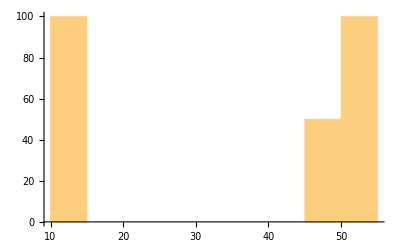

```mathematica
Histogram[myData,10]
```

#### Visualize Dynamically!

The serial stream is a stream of bytes. Well actually, they are bits, which make up the bytes. For the most part, each set of eight bits (0s and 1s) is a single character, a byte. It is important to note that the data arriving via the serial stream is not composed of numbers, per se. However, Mathematica knows how to convert the byte stream to numbers, integers in this case.

We can set Mathematica up to continuously or dynamically read the serial stream from the Arduino using a function called Dynamic[] and Refresh[]. 

Later we will see that we can reverse the serial stream and write to the Arduino. Using the same function, Dynamic[], used here, we can send values from controls in a Mathematica notebook to control physical things like an LED or servo motor attached to the Arduino. Cool. Execute the following code. Make sure your myArduino  object is working. You should be able to change the value in progress indicator by turning your potentiometer back and forth.

```mathematica
ProgressIndicator[Dynamic[Refresh[DeviceRead[myArduino],UpdateInterval-> 5]],{0,100}]
```

Or use these gauges:

```mathematica
HorizontalGauge[Dynamic[Refresh[DeviceRead[myArduino],UpdateInterval-> 5]],{0,100}]
```

```mathematica
ThermometerGauge[Dynamic[Refresh[DeviceRead[myArduino],UpdateInterval-> 5]],{0,100}]
```

```mathematica
AngularGauge[Dynamic[Refresh[DeviceRead[myArduino],UpdateInterval-> 5]],{0,100}]
```

Steam Punk Mathematica!

#### Disconnecting

Finally, when we are ready to disconnect Mathematica from the serial data stream we can invoke the DeviceClose[] function naming the serial connection object, myArduino, within the square brackets. Once the function is run, the ProgressIndicator will stop updating and the myArduino object will be destroyed.

To restart the connection you need to invoke the DeviceOpen[] function again creating an object in the process like you did above with myArduino. Once you execute DeviceClose[], you will notice that your DeviceObject indicates “not connected.”

```mathematica
DeviceClose[myArduino];
```

#### Recap

To recap, you will need to execute the following code on the Arduino and in Mathematica.

Arduino

int potPin = 0;

void setup () 
{
	Serial.begin (9600);
}

void loop () 
{
	int reading  = analogRead (potPin);
	Serial.println (reading);
	delay (500);
}

Mathematica

To dynamically display streaming values you need two lines of code.

	myArduino = DeviceOpen["Serial", "device or path to /dev file"];
	ProgressIndicator[Dynamic[Refresh[myArduino, UpdateInterval -> 0.5]], {0, 100}]

Short and sweet.

The ProgressIndicator[] is only one of many possibilities to display your data. The data could be displayed in an analog gauge or as a graph of one kind or another. If you added a time stamp to serialDataRead so that every time the serial stream was read a datetime and pot value would be returned, you could construct an automatically updating timeseries chart of the pot value.

## Lab notebook

## References

Code derived from:

Arduino Group (2014) analogRead(). http://arduino.cc/en/Reference/AnalogRead.

Arduino Group (2014) Knob.http://arduino.cc/en/Tutorial/Knob.

Monk, Simon (2012) Arduino Lesson 8. Analog Inputs. https://learn.adafruit.com/adafruit-arduino-lesson-8-analog-inputs.

Turkel, William (2011) Connecting Arduino to Mathematica on Mac OSX with SerialIO. http://williamjturkel.net/2011/12/25/connecting-arduino-to-mathematica-on-mac-os-x-with-serialio/.